```mathematica
a14= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/average0.14.dat"]
```

```mathematica
a29= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/average0.29.dat"]
```

```mathematica
a43= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/average0.43.dat"]
```

```mathematica
a72= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/average0.72.dat"]
```

```mathematica
a86= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/average0.86.dat"]
```

```mathematica
a101= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/average1.01.dat"]
```

```mathematica
trans14= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/transmission0.14.dat"]
```

```mathematica
trans29= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/transmission0.29.dat"]
```

```mathematica
trans43= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/transmission0.43.dat"]
```

```mathematica
trans72= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/transmission0.72.dat"]
```

```mathematica
trans86:=trans86= Import["/home/shardul/PhD_new/PhD/fwi/AGNR/DFT/Data/transmission0.86.dat"]
```

```mathematica
trans101= Import["/home/shardulmukim/PhD/fwi/AGNR/DFT/Data/transmission1.01.dat"]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter1/transmission_dft.dat",Table[{trans86[[x]][[1]],trans86[[x]][[2]]},{x,495}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter1/transmission_dft.dat

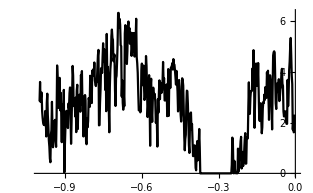

```mathematica
Show[(*ListLinePlot[Table[{a14[[x]][[1]],a14[[x]][[2]]},{x,495}],PlotStyle->Red],ListLinePlot[Table[{a43[[x]][[1]],a43[[x]][[2]]},{x,495}],PlotStyle->Blue],*)ListLinePlot[Table[{trans86[[x]][[1]],trans86[[x]][[2]]},{x,495}],PlotStyle->Black]]
```

```mathematica
NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans14[[x]][[2]]-a14[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.02}]
```

0.114619

```mathematica
Misfit[n_]:= Module[{},
ρ1=NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans[[n]][[x]][[2]]-a14[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.002}];
ρ2=NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans[[n]][[x]][[2]]-a29[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.002}];ρ3=NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans[[n]][[x]][[2]]-a43[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.002}];ρ4=NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans[[n]][[x]][[2]]-a72[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.002}];ρ5=NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans[[n]][[x]][[2]]-a86[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.002}];ρ6=NIntegrate[Interpolation[Table[{a14[[x]][[1]],(trans[[n]][[x]][[2]]-a101[[x]][[2]])^2},{x,495}]][ω],{ω,-1,-0.002}];
{{0.14,ρ1},{0.29,ρ2},{0.43,ρ3},{0.72,ρ4},{0.86,ρ5},{1.01,ρ6}}]
```

```mathematica
trans={trans14,trans29,trans43,trans72,trans86,trans101}
```

{{{-1.,5.2127,2.50967,0.19140540-157,0.76267078-158,2.70303,0.20615208-157,0.76267078-158,4,4},{-0.99798,5.77433,2.78491,0.61503769-157,0.22084626-157,2.98942,0.66020210-157,0.22084626-157,4,4},{-0.99596,5.59461,2.70938,0.17326596-156,0.63950362-157,2.88523,0.18451146-156,0.63950362-157,4,4},491,{-0.0020202,3.59353,1.78848,5.08923×10^-65,2.84555×10^-65,1.80505,5.13635×10^-65,2.84555×10^-65,3,3},{0.,3.94498,1.97859,1.94433×10^-65,9.82684×10^-66,1.96639,1.93234×10^-65,9.82684×10^-66,3,3}},{1},1,1,{1},{1}}
 |  |  |  |

```mathematica
Misfit[5]
```

{{0.14,5.94139},{0.29,2.1436},{0.43,0.888858},{0.72,0.295006},{0.86,0.224525},{1.01,0.605349}}

```mathematica
Interpolation[Misfit[5],InterpolationOrder->3]
```

InterpolatingFunction[…]

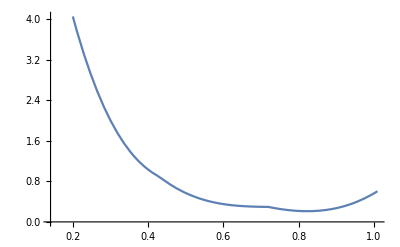

```mathematica
Plot[%18[x],{x,0.14,1.01}]
```

```mathematica
%19[1]
```

Null[1]

```mathematica
Show[ListLinePlot[Table[{x,%32[x]},{x,Range[0.76,0.91,0.00001]}]],ListPlot[{{0.8,%32[0.8]}},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[Plot[%43[x],{x,0.6,0.9},PlotStyle->Blue],PlotRange->{{0.6,1.01},{0,1}},Frame->True]
```

-Graphics-

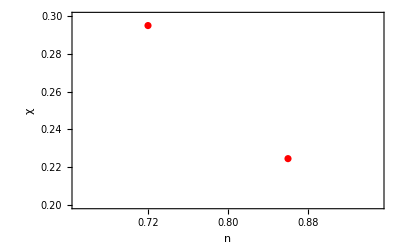

```mathematica
Show[Show[Plot[%77[x],{x,0.14,1.01},PlotStyle->Blue],ListPlot[Misfit[5],PlotStyle->Red],PlotRange->{{0.65,0.95},{0.2,0.3}},Frame->True],Axes->False,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

```mathematica
Show[Show[ListLinePlot[Table[{x,%32[x]},{x,Range[0.73,0.91,0.00001]}],PlotStyle->Blue],ListPlot[{{0.8,%32[0.8]}},PlotStyle->Red],Frame->True],FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

-Graphics-